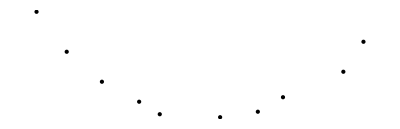

```mathematica
n=10;
X={-3,-2.4,-1.7,-0.96,-0.55,0.65,1.4,1.9,3.1,3.5};
Y={2.5,1.7,1.1,0.7,0.45,0.39,0.5,0.79,1.3,1.9};
Graphics[Point[{{X[[1]],Y[[1]]},{X[[2]],Y[[2]]},{X[[3]],Y[[3]]},{X[[4]],Y[[4]]},{X[[5]],Y[[5]]},
{X[[6]],Y[[6]]},{X[[7]],Y[[7]]},{X[[8]],Y[[8]]},{X[[9]],Y[[9]]},{X[[10]],Y[[10]]}}]]
```

```mathematica
T=Table[0,n];
Z=T;
For[i=1,i≤n,i++,{T[[i]]=Re[Log[X[[i]]]];Z[[i]]=Re[Log[Y[[i]]]]}];
Print[T];
Print[Z];
Graphics[Point[{{T[[1]],Z[[1]]},{T[[2]],Z[[2]]},{T[[3]],Z[[3]]},{T[[4]],Z[[4]]},{T[[5]],Z[[5]]},
{T[[6]],Z[[6]]},{T[[7]],Z[[7]]},{T[[8]],Z[[8]]},{T[[9]],Z[[9]]},{T[[10]],Z[[10]]}}]]
```

{Log[3],0.875469,0.530628,-0.040822,-0.597837,-0.430783,0.336472,0.641854,1.1314,1.25276}

{0.916291,0.530628,0.0953102,-0.356675,-0.798508,-0.941609,-0.693147,-0.235722,0.262364,0.641854}

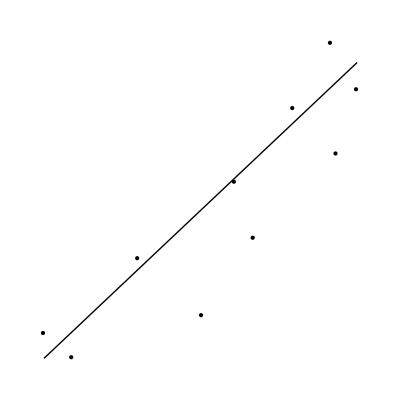

```mathematica
SumX1=0;
For[i=1,i≤n,i++,SumX1+=X[[i]]];
SumX2=0
For[i=1,i≤n,i++,SumX2+=X[[i]]^2];
SumX3=0;
For[i=1,i≤n,i++,SumX3+=X[[i]]^3];
SumX4=0;
For[i=1,i≤n,i++,SumX4+=X[[i]]^4];
SumY=0;
For[i=1,i≤n,i++,SumY+=Y[[i]]];
SumXY=0;
For[i=1,i≤n,i++,SumXY+=X[[i]]*Y[[i]]];
SumX2Y=0;
For[i=1,i≤n,i++,SumX2Y+=X[[i]]^2*Y[[i]]];
```

```mathematica
Solve[n*a0+a1*SumX1+a2*SumX2==SumY&&a0*SumX1+a1*SumX2+a2*SumX3==SumXY&&a0*SumX2+a1*SumX3+a2*SumX4==SumX2Y,{a0,a1,a2},Reals];
```

```mathematica
{a0,a1,a2}/.{{a0->0.38168347694310145,a1->-0.17073901517131937,a2->0.16787865840872968}}
```

{{0.381683,-0.170739,0.167879}}

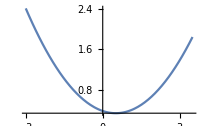
Show[-Graphics-,Point[{{-3,2.5},{-2.4,1.7},{-1.7,1.1},{-0.96,0.7},{-0.55,0.45},{0.65,0.39},{1.4,0.5},{1.9,0.79},{3.1,1.3},{3.5,1.9}}]]

```mathematica
f1[x_]:=0.16787865840872968*x^2-0.17073901517131937*x+0.38168347694310145;
Show[Plot[f1[x],{x,-3,3.5}],ListPlot[{{X[[1]],Y[[1]]},{X[[2]],Y[[2]]},{X[[3]],Y[[3]]},{X[[4]],Y[[4]]},{X[[5]],Y[[5]]},
{X[[6]],Y[[6]]},{X[[7]],Y[[7]]},{X[[8]],Y[[8]]},{X[[9]],Y[[9]]},{X[[10]],Y[[10]]}}]]
```